# Dynamical Systems Analysis of Ellis and Maartens’ Emergent Universe

## ϕ - ψ Expanding

```mathematica
V0=1;
```

```mathematica
H=Sqrt[(1/3)*(V0*(Exp[ϕ]-1)^2)+ψ^2/6]
```

√(1/3 (-1+ⅇ^ϕ)^2+ψ^2/6)

```mathematica
de1:=ϕ'=ψ
de2:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
(*de3:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)*)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ϕ,ψ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0,ψ→0},{ϕ→-∞,ψ→0}}

```mathematica
FP[1]={ϕ/.FPs[[1,1]],ψ/.FPs[[1,2]]};
FP[2]={ϕ/.FPs[[2,1]],ψ/.FPs[[2,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,2}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ϕ],D[de1,ψ]}, {D[de2,ϕ],D[de2,ψ]}}];
J//MatrixForm
```

(0 | 1
ⅇ^ϕ (2-4 ⅇ^ϕ-(√6 (-1+ⅇ^ϕ) ψ)/(√(2-4 ⅇ^ϕ+2 ⅇ^(2 ϕ)+ψ^2))) | -(√6 (1-2 ⅇ^ϕ+ⅇ^(2 ϕ)+ψ^2))/(√(2-4 ⅇ^ϕ+2 ⅇ^(2 ϕ)+ψ^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,2}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 1
Indeterminate | Indeterminate) | Eigenvalues[{{0,1},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,1},{Indeterminate,Indeterminate}}]
(-∞
0) | (0 | 1
0 | -√3) | (-√3
0) | (-1/(√3) | 1
1 | 0)

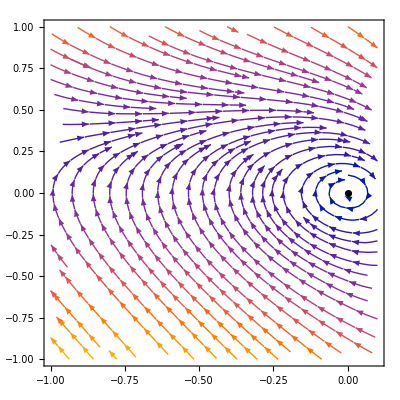

```mathematica
Show[StreamPlot[{de1,de2},{ϕ,-1,0.1},{ψ,-1,1}],FixedPointsPlot]
```

## ϕ - ψ Expanding Compactification

```mathematica
V0=1;
```

```mathematica
H=Sqrt[(1/3)*(V0*(Exp[Φ/Sqrt[(1-Φ^2)]]-1)^2)+(1/6)*(Ψ^2/(1-Ψ^2))]
```

√(1/3 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2 V0+Ψ^2/(6 (1-Ψ^2)))

```mathematica
de1:=Φ'=Ψ*((1-Φ^2)^(3/2))/Sqrt[1-Ψ^2]
de2:=Ψ'=-3*H*Ψ*(1-Ψ^2)-2*V0*Exp[Φ/Sqrt[1-Φ^2]]*(Exp[Φ/Sqrt[1-Φ^2]]-1)*(1-Ψ^2)^(3/2)
(*de3:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)*)
```

```mathematica
de2
```

-2 ⅇ^(Φ/(√(1-Φ^2))) (-1+ⅇ^(Φ/(√(1-Φ^2)))) (1-Ψ^2)^(3/2)-3 Ψ (1-Ψ^2) √(1/3 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(6 (1-Ψ^2)))

```mathematica
FPs=Solve[{de1==0,de2==0},{Φ,Ψ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Φ→0,Ψ→0}}

```mathematica
FP[1]={Φ/.FPs[[1,1]],Ψ/.FPs[[1,2]]};
```

```mathematica
(*Fixed points from compactification*)
FP[2]={1,1};
FP[3]={1,-1};
FP[4]={-1,1};
FP[5]={-1,-1};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,5}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,Φ],D[de1,Ψ]}, {D[de2,Φ],D[de2,Ψ]}}];
J//MatrixForm
```

(-(3 Φ √(1-Φ^2) Ψ)/(√(1-Ψ^2)) | ((1-Φ^2)^(3/2))/((1-Ψ^2)^(3/2))
(ⅇ^(Φ/(√(1-Φ^2))) (-1+Ψ^2) (√6 (-1+ⅇ^(Φ/(√(1-Φ^2)))) Ψ+2 (-1+2 ⅇ^(Φ/(√(1-Φ^2)))) √(1-Ψ^2) √(-4 ⅇ^(Φ/(√(1-Φ^2)))+2 ⅇ^((2 Φ)/(√(1-Φ^2)))+(-2+Ψ^2)/(-1+Ψ^2))))/((1-Φ^2)^(3/2) √(-4 ⅇ^(Φ/(√(1-Φ^2)))+2 ⅇ^((2 Φ)/(√(1-Φ^2)))+(-2+Ψ^2)/(-1+Ψ^2))) | 6 ⅇ^(Φ/(√(1-Φ^2))) (-1+ⅇ^(Φ/(√(1-Φ^2)))) Ψ √(1-Ψ^2)+(√(3/2) Ψ^2)/((-1+Ψ^2) √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2)))+√6 Ψ^2 √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2))+√(3/2) (-1+Ψ^2) √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,1}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 1
Indeterminate | Indeterminate) | Eigenvalues[{{0,1},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,1},{Indeterminate,Indeterminate}}]

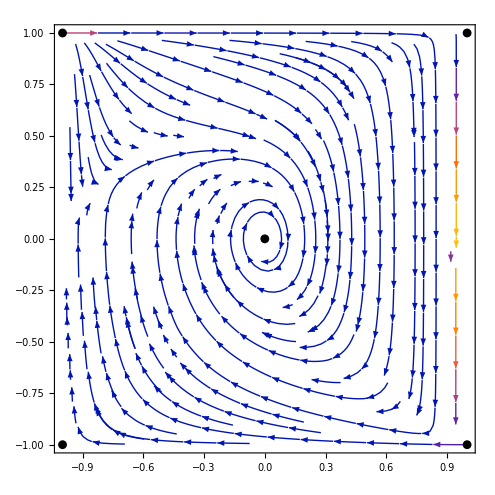

```mathematica
Show[StreamPlot[{de1,de2},{Φ,-1,1},{Ψ,-1,1}],FixedPointsPlot]
```

## ϕ - ψ Contracting

```mathematica
V0=1;
```

```mathematica
H=-Sqrt[(1/3)*(V0*(Exp[ϕ]-1)^2)+ψ^2/6]
```

-√(1/3 (-1+ⅇ^ϕ)^2+ψ^2/6)

```mathematica
de1:=ϕ'=ψ
de2:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
(*de3:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)*)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ϕ,ψ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0,ψ→0},{ϕ→-∞,ψ→0}}

```mathematica
FP[1]={ϕ/.FPs[[1,1]],ψ/.FPs[[1,2]]};
FP[2]={ϕ/.FPs[[2,1]],ψ/.FPs[[2,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,2}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ϕ],D[de1,ψ]}, {D[de2,ϕ],D[de2,ψ]}}];
J//MatrixForm
```

(0 | 1
ⅇ^ϕ (2-4 ⅇ^ϕ+(√6 (-1+ⅇ^ϕ) ψ)/(√(2-4 ⅇ^ϕ+2 ⅇ^(2 ϕ)+ψ^2))) | (√6 (1-2 ⅇ^ϕ+ⅇ^(2 ϕ)+ψ^2))/(√(2-4 ⅇ^ϕ+2 ⅇ^(2 ϕ)+ψ^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,2}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 1
Indeterminate | Indeterminate) | Eigenvalues[{{0,1},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,1},{Indeterminate,Indeterminate}}]
(-∞
0) | (0 | 1
0 | √3) | (√3
0) | (1/(√3) | 1
1 | 0)

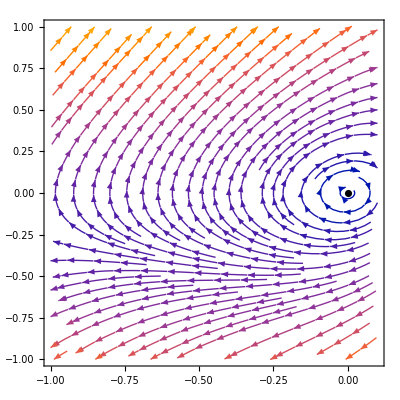

```mathematica
Show[StreamPlot[{de1,de2},{ϕ,-1,0.1},{ψ,-1,1}],FixedPointsPlot]
```

## ϕ - ψ Contracting Compactification

```mathematica
Solve[Sqrt[V0/3+Ψ^2/(6*(1-Ψ^2))]==0,Ψ]
```

{{Ψ→-√2},{Ψ→√2}}

```mathematica
FindRoot[{de1==0,de2==0},{Ψ,-0.2},{Φ,-.9}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Ψ→-0.0000459755,Φ→-0.995107}

```mathematica
FindRoot[{-3*(Sqrt[(1/3)*((Exp[Φ/Sqrt[(1-Φ^2)]]-1)^2)+(1/6)*(Ψ^2/(1-Ψ^2))])*Ψ*(1-Ψ^2)-2*Exp[Φ/Sqrt[1-Φ^2]]*(Exp[Φ/Sqrt[1-Φ^2]]-1)*(1-Ψ^2)^(3/2)==0,Ψ*((1-Φ^2)^(3/2))/Sqrt[1-Ψ^2]==0},{Ψ,0.2},{Φ,-.9}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Ψ→0.0000459755,Φ→-0.995107}

```mathematica
V0=1;
```

```mathematica
H=-Sqrt[(1/3)*(V0*(Exp[Φ/Sqrt[(1-Φ^2)]]-1)^2)+(1/6)*(Ψ^2/(1-Ψ^2))]
```

-√(1/3 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(6 (1-Ψ^2)))

```mathematica
de1:=Φ'=Ψ*((1-Φ^2)^(3/2))/Sqrt[1-Ψ^2]
de2:=Ψ'=-3*H*Ψ*(1-Ψ^2)-2*V0*Exp[Φ/Sqrt[1-Φ^2]]*(Exp[Φ/Sqrt[1-Φ^2]]-1)*(1-Ψ^2)^(3/2)
(*de3:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)*)
```

```mathematica
de2
```

-2 ⅇ^(Φ/(√(1-Φ^2))) (-1+ⅇ^(Φ/(√(1-Φ^2)))) (1-Ψ^2)^(3/2)+3 Ψ (1-Ψ^2) √(1/3 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(6 (1-Ψ^2)))

```mathematica
FPs=Solve[{de1==0,de2==0},{Φ,Ψ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Φ→0,Ψ→0}}

```mathematica
FP[1]={Φ/.FPs[[1,1]],Ψ/.FPs[[1,2]]};
```

```mathematica
(*Fixed points from compactification*)
FP[2]={1,1};
FP[3]={1,-1};
FP[4]={-1,1};
FP[5]={-1,-1};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,5}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,Φ],D[de1,Ψ]}, {D[de2,Φ],D[de2,Ψ]}}];
J//MatrixForm
```

(-(3 Φ √(1-Φ^2) Ψ)/(√(1-Ψ^2)) | ((1-Φ^2)^(3/2))/((1-Ψ^2)^(3/2))
(ⅇ^(Φ/(√(1-Φ^2))) (-1+Ψ^2) (-√6 (-1+ⅇ^(Φ/(√(1-Φ^2)))) Ψ+2 (-1+2 ⅇ^(Φ/(√(1-Φ^2)))) √(1-Ψ^2) √(-4 ⅇ^(Φ/(√(1-Φ^2)))+2 ⅇ^((2 Φ)/(√(1-Φ^2)))+(-2+Ψ^2)/(-1+Ψ^2))))/((1-Φ^2)^(3/2) √(-4 ⅇ^(Φ/(√(1-Φ^2)))+2 ⅇ^((2 Φ)/(√(1-Φ^2)))+(-2+Ψ^2)/(-1+Ψ^2))) | 6 ⅇ^(Φ/(√(1-Φ^2))) (-1+ⅇ^(Φ/(√(1-Φ^2)))) Ψ √(1-Ψ^2)-(√(3/2) Ψ^2)/((-1+Ψ^2) √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2)))-√6 Ψ^2 √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2))-√(3/2) (-1+Ψ^2) √(2 (-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,1}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 1
Indeterminate | Indeterminate) | Eigenvalues[{{0,1},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,1},{Indeterminate,Indeterminate}}]

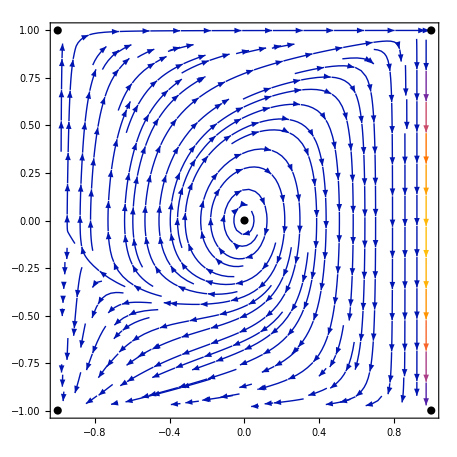

```mathematica
Show[StreamPlot[{de1,de2},{Φ,-1,1},{Ψ,-1,1}],FixedPointsPlot]
```

## ϕ - H: ψ Positive

```mathematica
V0=1;
```

```mathematica
ψ=Sqrt[6*H^2-2*V0*(Exp[ϕ]-1)^2]
```

√(-2 (-1+ⅇ^ϕ)^2+6 H^2)

```mathematica
de1:=ϕ'=ψ
(*de2:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)*)
de2:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ϕ,H}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H→-(-1+ⅇ^ϕ)/(√3)},{H→(-1+ⅇ^ϕ)/(√3)}}

```mathematica
FP[1]={ϕ,H/.FPs[[1,1]]};
FP[2]={ϕ,H/.FPs[[2,1]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,2}];
```

```mathematica
FixedLine=Plot[{(-1+ⅇ^ϕ)/(√3),-(-1+ⅇ^ϕ)/(√3)},{ϕ,-1,1}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ϕ],D[de1,H]}, {D[de2,H],D[de2,H]}}];
J//MatrixForm
```

(-(2 ⅇ^ϕ (-1+ⅇ^ϕ))/(√(-2 (-1+ⅇ^ϕ)^2+6 H^2)) | (6 H)/(√(-2 (-1+ⅇ^ϕ)^2+6 H^2))
-6 H | -6 H)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,2}];
```

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(ϕ
-(-1+ⅇ^ϕ)/(√3)) | (ComplexInfinity | ComplexInfinity
2 √3 (-1+ⅇ^ϕ) | 2 √3 (-1+ⅇ^ϕ)) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{2 √3 (-1+ⅇ^ϕ),2 √3 (-1+ⅇ^ϕ)}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{2 √3 (-1+ⅇ^ϕ),2 √3 (-1+ⅇ^ϕ)}}]
(ϕ
(-1+ⅇ^ϕ)/(√3)) | (ComplexInfinity | ComplexInfinity
-2 √3 (-1+ⅇ^ϕ) | -2 √3 (-1+ⅇ^ϕ)) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{-2 √3 (-1+ⅇ^ϕ),-2 √3 (-1+ⅇ^ϕ)}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{-2 √3 (-1+ⅇ^ϕ),-2 √3 (-1+ⅇ^ϕ)}}]

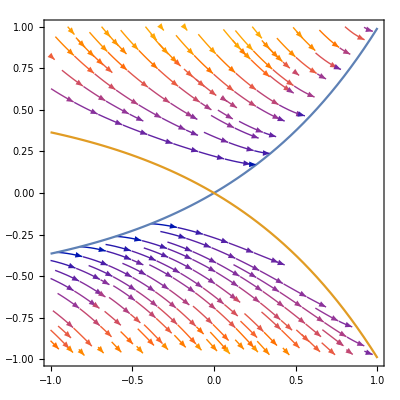

```mathematica
Show[StreamPlot[{de1,de2},{ϕ,-1,1},{H,-1,1}],FixedLine]
```

## ϕ - H: ψ Negative

```mathematica
V0=1;
```

```mathematica
ψ=-Sqrt[6*H^2-2*V0*(Exp[ϕ]-1)^2]
```

-√(-2 (-1+ⅇ^ϕ)^2+6 H^2)

```mathematica
de1:=ϕ'=ψ
(*de2:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)*)
de2:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ϕ,H}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H→-(-1+ⅇ^ϕ)/(√3)},{H→(-1+ⅇ^ϕ)/(√3)}}

```mathematica
FP[1]={ϕ,H/.FPs[[1,1]]};
FP[2]={ϕ,H/.FPs[[2,1]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,2}];
```

```mathematica
FixedLine=Plot[{(-1+ⅇ^ϕ)/(√3),-(-1+ⅇ^ϕ)/(√3)},{ϕ,-1,1}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ϕ],D[de1,H]}, {D[de2,ϕ],D[de2,H]}}];
J//MatrixForm
```

(0 | -3 ψ+H (-12-6/(√(3 H^2-ψ^2/2)))
0 | 0)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ϕ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,2}];
```

Part::partw: Part 2 of {{0,0}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(ϕ
-(-1+ⅇ^ϕ)/(√3)) | (ComplexInfinity | ComplexInfinity
2 √3 (-1+ⅇ^ϕ) | 2 √3 (-1+ⅇ^ϕ)) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{2 √3 (-1+ⅇ^ϕ),2 √3 (-1+ⅇ^ϕ)}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{2 √3 (-1+ⅇ^ϕ),2 √3 (-1+ⅇ^ϕ)}}]
(ϕ
(-1+ⅇ^ϕ)/(√3)) | (ComplexInfinity | ComplexInfinity
-2 √3 (-1+ⅇ^ϕ) | -2 √3 (-1+ⅇ^ϕ)) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{-2 √3 (-1+ⅇ^ϕ),-2 √3 (-1+ⅇ^ϕ)}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{-2 √3 (-1+ⅇ^ϕ),-2 √3 (-1+ⅇ^ϕ)}}]

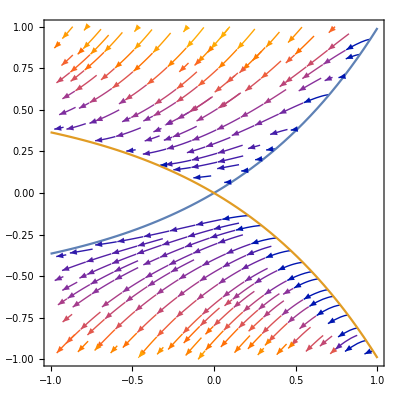

```mathematica
Show[StreamPlot[{de1,de2},{ϕ,-1,1},{H,-1,1}],FixedLine]
```

## ψ - H:

```mathematica
V0=1;
```

```mathematica
ϕ=Log[1+Sqrt[(1/V0)*(3*H^2-ψ^2/2)]]
```

Log[1+√(3 H^2-ψ^2/2)]

```mathematica
(*de1:=ϕ'=ψ*)
de1:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
de2:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ψ,H}]
```

{{ψ→0,H→0}}

```mathematica
FP[1]={ψ/.FPs[[1,1]],H/.FPs[[1,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,1}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ψ],D[de1,H]}, {D[de2,ψ],D[de2,H]}}];
J//MatrixForm
```

(-3 H+ψ (2+1/(√(3 H^2-ψ^2/2))) | -3 ψ+H (-12-6/(√(3 H^2-ψ^2/2)))
-ψ | 0)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,1}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

## ψ - H:

```mathematica
V0=1;
```

```mathematica
ϕ=Log[1+Sqrt[(1/V0)*(3*H^2-ψ^2/2)]]
```

Log[1+√(3 H^2-ψ^2/2)]

```mathematica
(*de1:=ϕ'=ψ*)
de1:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
de2:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ψ,H}]
```

{{ψ→0,H→0}}

```mathematica
FP[1]={ψ/.FPs[[1,1]],H/.FPs[[1,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,1}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ψ],D[de1,H]}, {D[de2,ψ],D[de2,H]}}];
J//MatrixForm
```

(-3 H+ψ (2+1/(√(3 H^2-ψ^2/2))) | -3 ψ+H (-12-6/(√(3 H^2-ψ^2/2)))
-ψ | 0)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,1}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | 0) | Eigenvalues[{{Indeterminate,Indeterminate},{0,0}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,0}}]

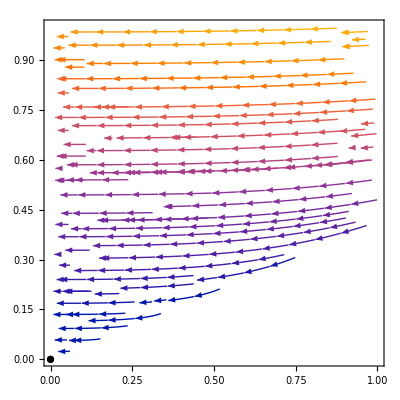

```mathematica
Show[StreamPlot[{de1,de2},{ψ,0,1},{H,0,1}],FixedPointsPlot]
```

## ψ - H:

```mathematica
V0=1;
```

```mathematica
ϕ=Log[1-Sqrt[(1/V0)*(3*H^2-ψ^2/2)]]
```

Log[1-√(3 H^2-ψ^2/2)]

```mathematica
(*de1:=ϕ'=ψ*)
de1:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
de2:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
FPs=Solve[{de1==0,de2==0},{ψ,H}]
```

{{ψ→0,H→0},{ψ→0,H→-1/(√3)},{ψ→0,H→1/(√3)}}

```mathematica
FP[1]={ψ/.FPs[[1,1]],H/.FPs[[1,2]]};
FP[2]={ψ/.FPs[[2,1]],H/.FPs[[2,2]]};
FP[3]={ψ/.FPs[[3,1]],H/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,3}];
```

```mathematica
FixedPointsPlot=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ψ],D[de1,H]}, {D[de2,ψ],D[de2,H]}}];
J//MatrixForm
```

(-3 H+ψ (2-1/(√(3 H^2-ψ^2/2))) | -3 ψ+H (-12+6/(√(3 H^2-ψ^2/2)))
-ψ | 0)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],H->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,3}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | 0) | Eigenvalues[{{Indeterminate,Indeterminate},{0,0}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,0}}]
(0
-1/(√3)) | (√3 | 2 √3
0 | 0) | (√3
0) | (1 | 0
-2 | 1)
(0
1/(√3)) | (-√3 | -2 √3
0 | 0) | (-√3
0) | (1 | 0
-2 | 1)

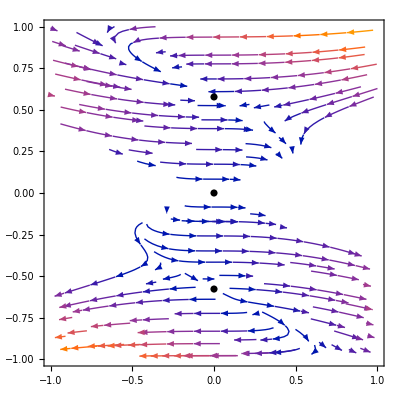

```mathematica
Show[StreamPlot[{de1,de2},{ψ,-1,1},{H,-1,1}],FixedPointsPlot]
```

## 3D Phase Space

```mathematica
de1:=ϕ'=ψ
de2:=ψ'=-3*H*ψ-2*V0*Exp[ϕ]*(Exp[ϕ]-1)
de3:=H'=-H^2-(1/3)*(ψ^2-V0*(Exp[ϕ]-1)^2)
```

```mathematica
V0=1;
```

```mathematica
FPs=Solve[{de1==0,de2==0,de3==0},{ϕ,ψ,H}]
```

{{ψ→0,H→0,ϕ→ConditionalExpression[2 ⅈ π C[1], C[1]∈ℤ]}}

```mathematica
FP[1]={ϕ/.FPs[[1,3]],ψ/.FPs[[1,1]],H/.FPs[[1,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,1}];
```

```mathematica
FixedPointsPlot=ListPointPlot3D[FixedPoints,PlotStyle->Black]
```

-Graphics3D-

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,ϕ],D[de1,ψ],D[de1,H]}, {D[de2,ϕ],D[de2,ψ],D[de2,H]},{D[de3,ϕ],D[de3,ψ],D[de3,H]}}];
J//MatrixForm
```

(0 | 1 | 0
-2 ⅇ^ϕ (-1+2 ⅇ^ϕ) | -3 H | -3 ψ
2/3 ⅇ^ϕ (-1+ⅇ^ϕ) | -(2 ψ)/3 | -2 H)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],H->FixedPoints[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],H->FixedPoints[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ϕ->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],H->FixedPoints[[i,3]]}]]//MatrixForm},{i,1,1}];
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(ConditionalExpression[2 ⅈ π C[1], C[1]∈ℤ]
0
0) | (0 | 1 | 0
ConditionalExpression[-2, C[1]∈ℤ] | 0 | 0
ConditionalExpression[0, C[1]∈ℤ] | 0 | 0) | Eigenvalues[{{0,1,0},{ConditionalExpression[-2, C[1]∈ℤ],0,0},{ConditionalExpression[0, C[1]∈ℤ],0,0}}] | Eigenvectors[{{0,1,0},{ConditionalExpression[-2, C[1]∈ℤ],0,0},{ConditionalExpression[0, C[1]∈ℤ],0,0}}]

```mathematica
StreamPlot3D[{de1,de2,de3},{ϕ,-1,1},{ψ,-1,1},{H,-1,1}]
```

-Graphics3D-

```mathematica
ψ=-Sqrt[6*H^2-2*V0*(Exp[ϕ]-1)^2]
```

```mathematica
de1t:=ϕ1'[t]==ψ1[t]
de2t:=ψ1'[t]==-3*H1[t]*ψ1[t]-2*V0*Exp[ϕ1[t]]*(Exp[ϕ1[t]]-1)
de3t:=H1'[t]==-H1[t]^2-(1/3)*(ψ1[t]^2-V0*(Exp[ϕ1[t]]-1)^2)
```

```mathematica
traj[ϕ0_,H0_,β_]=NDSolve[{de1t,de2t,de3t,ϕ1[0]==ϕ0,ψ1[0]==β*Sqrt[6*H0^2-2*V0*(Exp[ϕ0]-1)^2],H1[0]==H0},{ϕ1,ψ1,H1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition H0 is not a number or a rectangular array of numbers.

NDSolve[{ϕ1'[t]==ψ1[t],ψ1'[t]==-2 ⅇ^ϕ1[t] (-1+ⅇ^ϕ1[t])-3 H1[t] ψ1[t],H1'[t]==-H1[t]^2+1/3 ((-1+ⅇ^ϕ1[t])^2-ψ1[t]^2),ϕ1[0]==ϕ0,ψ1[0]==√(-2 (-1+ⅇ^ϕ0)^2+6 H0^2) β,H1[0]==H0},{ϕ1,ψ1,H1},{t,-100,100}]

```mathematica
sol[1]=traj[0.5,-0.5,-1]
```

NDSolve::ndsz: At t == 0.732058, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],H1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[0.5,0.5,1]
```

NDSolve::ndsz: At t == -0.732058, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],H1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[0.8,0.8,1]
```

NDSolve::ndsz: At t == -0.50074, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],H1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj[0.8,-0.8,-1]
```

NDSolve::ndsz: At t == 0.50074, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],H1→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj[0.2,0.2,1]
```

NDSolve::ndsz: At t == -1.96935, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],H1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
traj[1]=ParametricPlot3D[Evaluate[{{ϕ1[t],ψ1[t],H1[t]}}/.sol[1],{t,-100,0.731},PlotStyle -> {{Black}}],PlotPoints->500];
```

```mathematica
traj[2]=ParametricPlot3D[Evaluate[{{ϕ1[t],ψ1[t],H1[t]}}/.sol[2],{t,-0.731,100},PlotStyle -> {{Black}}],PlotPoints->500];
```

```mathematica
traj[3]=ParametricPlot3D[Evaluate[{{ϕ1[t],ψ1[t],H1[t]}}/.sol[3],{t,-0.5,100},PlotStyle -> {{Black}}],PlotPoints->500];
```

```mathematica
traj[4]=ParametricPlot3D[Evaluate[{{ϕ1[t],ψ1[t],H1[t]}}/.sol[4],{t,-100,0.5},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
traj[5]=ParametricPlot3D[Evaluate[{{ϕ1[t],ψ1[t],H1[t]}}/.sol[5],{t,-1.96,100},PlotStyle -> {{Black}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajectories=Table[traj[i],{i,1,5}];
```

```mathematica
V0=1
```

1

```mathematica
FlatSurf=ContourPlot3D[{H==Sqrt[(1/3)*((Exp[ϕ]-1)^2)+(ψ^2/6)],H==-Sqrt[(1/3)*((Exp[ϕ]-1)^2)+(ψ^2/6)]},{ϕ,-1,1},{ψ,-1,1},{H,-1,1},ContourStyle->{{Darker[Green],Opacity[0.5]}}]
```

-Graphics3D-

```mathematica
(*Show the x-y-z phase space*)
Show[trajectories,FlatSurf,PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

## Compactification

```mathematica
de1:=Φ'=Ψ*((1-Φ^2)^(3/2))/Sqrt[1-Ψ^2]
de2:=Ψ'=-3*U*Ψ*(1-Ψ^2)/Sqrt[1-U^2]-2*V0*Exp[Φ/Sqrt[1-Φ^2]]*(Exp[Φ/Sqrt[1-Φ^2]]-1)
de3:=U'=-U^2*Sqrt[1-U^2]-((1-U^2)^(3/2)/3)*(Ψ^2/(1-Ψ^2)-V0*(Exp[Φ/Sqrt[1-Φ^2]]-1)^2)
```

```mathematica
V0=1;
```

```mathematica
FPs=Solve[{de1==0,de2==0,de3==0},{Φ,Ψ,U}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Φ→0,Ψ→0,U→0}}

```mathematica
FP[1]={Φ/.FPs[[1,1]],Ψ/.FPs[[1,2]],U/.FPs[[1,3]]};
```

```mathematica
(*Fixed points from compactification*)
FP[2]={-1,0,0};
FP[3]={0,0,1};
FP[4]={0,0,-1};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,4}];
```

```mathematica
FixedPointsPlot=ListPointPlot3D[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[de1,Φ],D[de1,Ψ],D[de1,U]}, {D[de2,Φ],D[de2,Ψ],D[de2,U]},{D[de3,Φ],D[de3,Ψ],D[de3,U]}}];
J//MatrixForm
```

(-(3 Φ √(1-Φ^2) Ψ)/(√(1-Ψ^2)) | ((1-Φ^2)^(3/2))/((1-Ψ^2)^(3/2)) | 0
-(2 ⅇ^(Φ/(√(1-Φ^2))) (-1+2 ⅇ^(Φ/(√(1-Φ^2)))))/((1-Φ^2)^(3/2)) | (3 U (-1+3 Ψ^2))/(√(1-U^2)) | (3 Ψ (-1+Ψ^2))/((1-U^2)^(3/2))
(2 ⅇ^(Φ/(√(1-Φ^2))) (-1+ⅇ^(Φ/(√(1-Φ^2)))) (1-U^2)^(3/2))/(3 (1-Φ^2)^(3/2)) | -(2 (1-U^2)^(3/2) Ψ)/(3 (-1+Ψ^2)^2) | (U (U^2+2 (-1+U^2)+(1-U^2) (-(-1+ⅇ^(Φ/(√(1-Φ^2))))^2+Ψ^2/(1-Ψ^2))))/(√(1-U^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],U->FixedPoints[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],U->FixedPoints[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{Φ->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],U->FixedPoints[[i,3]]}]]//MatrixForm},{i,1,1}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0
0) | (0 | 1 | 0
-2 | 0 | 0
0 | 0 | 0) | (ⅈ √2
-ⅈ √2
0) | (-ⅈ/(√2) | 1 | 0
ⅈ/(√2) | 1 | 0
0 | 0 | 1)

```mathematica
de1t:=Φ1'[t]==Ψ1[t]*((1-Φ1[t]^2)^(3/2))/Sqrt[1-Ψ1[t]^2]
de2t:=Ψ1'[t]==-3*U1[t]*Ψ1[t]*(1-Ψ1[t]^2)/Sqrt[1-U1[t]^2]-2*V0*Exp[Φ1[t]/Sqrt[1-Φ1[t]^2]]*(Exp[Φ1[t]/Sqrt[1-Φ1[t]^2]]-1)
de3t:=U1'[t]==-U1[t]^2*Sqrt[1-U1[t]^2]-((1-U1[t]^2)^(3/2)/3)*(Ψ1[t]^2/(1-Ψ1[t]^2)-V0*(Exp[Φ1[t]/Sqrt[1-Φ1[t]^2]]-1)^2)
```

### Flat Case

```mathematica
V0=1;
```

```mathematica
traj[Φ0_,β_,U0_]=NDSolve[{de1t,de2t,de3t,Φ1[0]==Φ0,Ψ1[0]==β*Sqrt[(6*U0^2/(1-U0^2)-2*V0*(Exp[Φ0/Sqrt[1-Φ0^2]]-1)^2)/(1+(6*U0^2/(1-U0^2)-2*V0*(Exp[Φ0/Sqrt[1-Φ0^2]]-1)^2))],U1[0]==U0},{Φ1,Ψ1,U1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition U0 is not a number or a rectangular array of numbers.

NDSolve[{Φ1'[t]==((1-Φ1[t]^2)^(3/2) Ψ1[t])/(√(1-Ψ1[t]^2)),Ψ1'[t]==-2 ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))) (-1+ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))))-(3 U1[t] Ψ1[t] (1-Ψ1[t]^2))/(√(1-U1[t]^2)),U1'[t]==-U1[t]^2 √(1-U1[t]^2)-1/3 (1-U1[t]^2)^(3/2) (-(-1+ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))))^2+Ψ1[t]^2/(1-Ψ1[t]^2)),Φ1[0]==Φ0,Ψ1[0]==√((-2 (-1+ⅇ^(Φ0/(√(1-Φ0^2))))^2+(6 U0^2)/(1-U0^2))/(1-2 (-1+ⅇ^(Φ0/(√(1-Φ0^2))))^2+(6 U0^2)/(1-U0^2))) β,U1[0]==U0},{Φ1,Ψ1,U1},{t,-100,100}]

```mathematica
sol[1]=traj[-0.2,-1,-0.2]
```

NDSolve::ndsz: At t == 3.54684, step size is effectively zero; singularity or stiff system suspected.

{{Φ1→InterpolatingFunction[…],Ψ1→InterpolatingFunction[…],U1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[0.2,1,0.2]
```

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.,1569.43,ComplexInfinity} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {-2.47795,1.,-0.995984,1.}.

{{Φ1→InterpolatingFunction[…],Ψ1→InterpolatingFunction[…],U1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
traj[1]=ParametricPlot3D[Evaluate[{{Φ1[t],Ψ1[t],U1[t]}}/.sol[1],{t,-100,3.44},PlotStyle -> {{Black}}],PlotPoints->800];
```

```mathematica
traj[2]=ParametricPlot3D[Evaluate[{{Φ1[t],Ψ1[t],U1[t]}}/.sol[2],{t,-2.36,100},PlotStyle -> {{Black}}],PlotPoints->800];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajectories=Table[traj[i],{i,1,2}];
```

```mathematica
FlatSurf=ContourPlot3D[{U==Sqrt[((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2))))/(1+((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2)))))],U==-Sqrt[((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2))))/(1+((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2)))))]},{Φ,-1,1},{Ψ,-1,1},{U,-1,1},ContourStyle->{{Darker[Green],Opacity[0.5]}}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajectories,FixedPointsPlot,FlatSurf,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{"ϕ","ψ","H"}]
```

-Graphics3D-

### Full Case

```mathematica
V0=1;
```

```mathematica
traj[Φ0_,Ψ0_,U0_]=NDSolve[{de1t,de2t,de3t,Φ1[0]==Φ0,Ψ1[0]==Ψ0,U1[0]==U0},{Φ1,Ψ1,U1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition U0 is not a number or a rectangular array of numbers.

NDSolve[{Φ1'[t]==((1-Φ1[t]^2)^(3/2) Ψ1[t])/(√(1-Ψ1[t]^2)),Ψ1'[t]==-2 ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))) (-1+ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))))-(3 U1[t] Ψ1[t] (1-Ψ1[t]^2))/(√(1-U1[t]^2)),U1'[t]==-U1[t]^2 √(1-U1[t]^2)-1/3 (1-U1[t]^2)^(3/2) (-(-1+ⅇ^(Φ1[t]/(√(1-Φ1[t]^2))))^2+Ψ1[t]^2/(1-Ψ1[t]^2)),Φ1[0]==Φ0,Ψ1[0]==Ψ0,U1[0]==U0},{Φ1,Ψ1,U1},{t,-100,100}]

```mathematica
sol[1]=traj[-.95,0.01,0.01]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,7.55208×10^-8} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {-37.4973,1.,-0.998293,1.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,5.3861×10^-10} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {37.0815,-1.,-0.998972,-1.}.

{{Φ1→InterpolatingFunction[…],Ψ1→InterpolatingFunction[…],U1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[0,0.01,0.99]
```

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.,8703.11,ComplexInfinity} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {-0.142301,1.,-0.528641,1.}.

{{Φ1→InterpolatingFunction[…],Ψ1→InterpolatingFunction[…],U1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[0,0.7,0]
```

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.,893.689,ComplexInfinity} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {-5.36229,1.,-0.970635,1.}.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.,-1919.74,ComplexInfinity} is not a list of numbers with dimensions {3} at {t,U1[t],Φ1[t],Ψ1[t]} = {3.1728,-1.,-0.996525,-1.}.

{{Φ1→InterpolatingFunction[…],Ψ1→InterpolatingFunction[…],U1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
traj[1]=ParametricPlot3D[Evaluate[{{Φ1[t],Ψ1[t],U1[t]}}/.sol[1],{t,0,37},PlotStyle -> {{Black}}],PlotPoints->800];
```

```mathematica
traj[2]=ParametricPlot3D[Evaluate[{{Φ1[t],Ψ1[t],U1[t]}}/.sol[2],{t,-0.141,100},PlotStyle -> {{Black}}],PlotPoints->800];
```

```mathematica
traj[3]=ParametricPlot3D[Evaluate[{{Φ1[t],Ψ1[t],U1[t]}}/.sol[3],{t,-5.35,3.16},PlotStyle -> {{Black}}],PlotPoints->800];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajectories=Table[traj[i],{i,3,3}];
```

```mathematica
FlatSurf=ContourPlot3D[{U==Sqrt[((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2))))/(1+((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2)))))],U==-Sqrt[((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2))))/(1+((1/3)*((Exp[Φ/Sqrt[1-Φ^2]]-1)^2)+(Ψ^2/(6*(1-Ψ^2)))))]},{Φ,-1,1},{Ψ,-1,1},{U,-1,1},ContourStyle->{{Darker[Green],Opacity[0.5]}}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajectories,FixedPointsPlot,FlatSurf,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{"ϕ","ψ","H"}]
```

-Graphics3D-